```mathematica
(* First attempt at regression NN for ABM *)
SetOptions[$FrontEnd,PrintPrecision->10]
```

```mathematica
(* ASSOCIATION 10 PARAMS -> SINGLE OUTPUT *)
(*ABMInputs=Import["/Users/thorsilver/Downloads/SocialCareOptimisation/ABM-for-social-care/hypercube10_GEMSA_inputs.csv"];*)
ABMInputs=Import["/Users/thorsilver/Downloads/SocialCareOptimisation/ABM-for-social-care/GEMSA - Expanded Replication/GEMSA data CSV2.csv"];
ABMOutputs=Import["/Users/thorsilver/Downloads/SocialCareOptimisation/ABM-for-social-care/GEMSA - Expanded Replication/GEMSA outputs CSV.csv"];
ABMOutputs=Function[x,x/1000]/@ABMOutputs;
(*ABMOutputs=Import["/Users/thorsilver/Downloads/SocialCareOptimisation/ABM-for-social-care/hypercube10 GEMSA outputs.csv"];*)
(*ABMOutputs=Partition[ABMOutputs,1];*)
ABMAssoc = AssociationThread[ABMInputs -> Flatten[ABMOutputs]];
ABMnewData=Dataset[ABMAssoc];
ABMNormal=Normal[ABMAssoc];
netData=Standardize[ABMNormal];
```

```mathematica
(*ABMData=SemanticImport["/Users/thorsilver/Downloads/SocialCareOptimisation/ABM-for-social-care/hypercube10_NN_ready.csv"];
DataAssoc=ABMData[All,<|"ageingParents"->1,"baseCareProb"->2,"retiredHours"->3,"ageOfRetirement"->4,"personCareProb"->5,"maleAgeCareScaling"->6,"femaleAgeCareScaling"->7,"childHours"->8,"homeAdultHours"->9,"workingAdultHours"->10,"ABMOutput"->11|>];
ABMDataSet=Dataset[DataAssoc];
testData=RandomSample[ABMAssoc,40];*)
```

```mathematica
(* Build a neural net to output a scalar *)
(*net2=NetChain[{LinearLayer[10],Tanh,150,DropoutLayer[],Tanh,1},"Input"->4,"Output"->"Scalar"]*)
 net3=NetChain[{LinearLayer[10],BatchNormalizationLayer[],ElementwiseLayer[Tanh],LinearLayer[100],BatchNormalizationLayer[],ElementwiseLayer[Tanh],DropoutLayer[],LinearLayer[1]},"Input"->4,"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
(* train net and return lowest validation loss *)
testData=RandomSample[ABMNormal,40];
{trainedNet,lowestVal}=NetTrain[net3,ABMNormal,{"TrainedNet","LowestValidationLoss"},Method-> {"SGD","L2Regularization"->0.05},ValidationSet->testData,MaxTrainingRounds->20000]
```

{NetChain[<>],20.7158}

```mathematica
testpoint=Part[ABMInputs,27]
```

{0.1,0.0008,40,60}

```mathematica
trainedNet[testpoint]
```

```mathematica
9.245174407958984
```

```mathematica
p= Predict[ABMNormal,Method->"GradientBoostedTrees"]
```

PredictorFunction[…]

```mathematica
testData=RandomSample[ABMNormal,80];
p[testpoint]
```

5.9517

```mathematica
pm=PredictorMeasurements[p,ABMNormal]
```

PredictorMeasurementsObject[…]

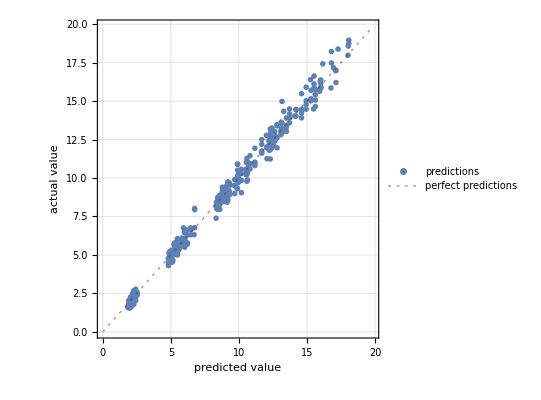

```mathematica
pm["ComparisonPlot"]
```

```mathematica
pmTest=PredictorMeasurements[p,testData]
```

PredictorMeasurementsObject[…]

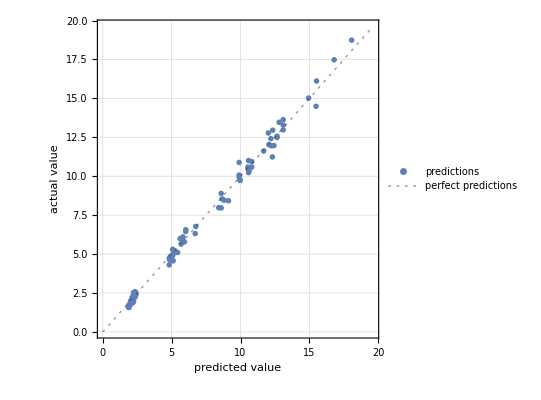

```mathematica
pmTest["ComparisonPlot"]
```

```mathematica
pNN= Predict[ABMNormal,Method->{"NeuralNetwork", "NetworkDepth"->5,"NetworkType"->"Convolutional", MaxTrainingRounds->8000}]
```

PredictorFunction[…]

```mathematica
pmNN=PredictorMeasurements[pNN,testData]
```

PredictorMeasurementsObject[…]

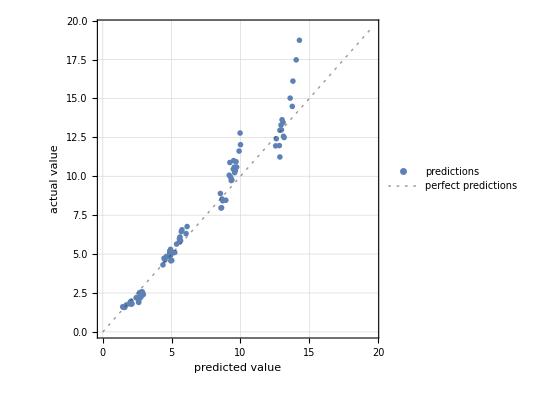

```mathematica
pmNN["ComparisonPlot"]
```

```mathematica
ABMInputs10=Import["/Users/thorsilver/Downloads/SocialCareOptimisation/ABM-for-social-care/lptau10round2_GEMSA_inputs.csv"];

ABMOutputs10=Import["/Users/thorsilver/Downloads/SocialCareOptimisation/ABM-for-social-care/lptau10round2 GEMSA outputs.csv"];
ABMOutputs10=Function[x,x/1000]/@ABMOutputs10;
ABMAssoc10 = AssociationThread[ABMInputs10 -> Flatten[ABMOutputs10]];
ABMnewData10=Dataset[ABMAssoc10];
ABMNormal10=Normal[ABMAssoc10];
```

```mathematica
testData10=RandomSample[ABMNormal10,80];
pXGT= Predict[ABMNormal10,Method->"GradientBoostedTrees"]
```

PredictorFunction[…]

```mathematica
pmXGT=PredictorMeasurements[pXGT,testData10]
```

PredictorMeasurementsObject[…]

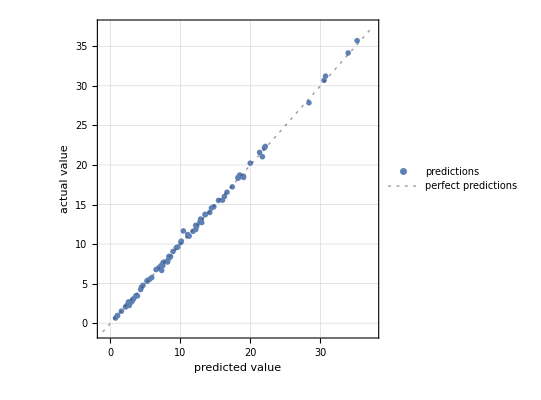

```mathematica
pmXGT["ComparisonPlot"]
```

```mathematica
pConvNN= Predict[ABMNormal10,Method->{"NeuralNetwork", "NetworkDepth"->3,"NetworkType"->"FullyConnected", "L2Regularization"->0.05, MaxTrainingRounds->16000}]
pmConvNN=PredictorMeasurements[pConvNN,testData10]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

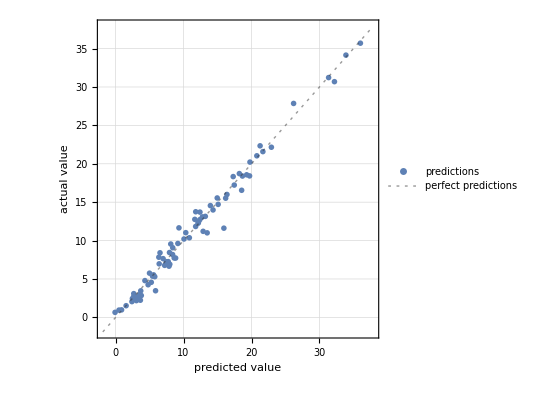

```mathematica
pmConvNN["ComparisonPlot"]
```

```mathematica
pGPE=Predict[ABMNormal10,Method->"GaussianProcess"]
pmGPE=PredictorMeasurements[pGPE,testData10]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

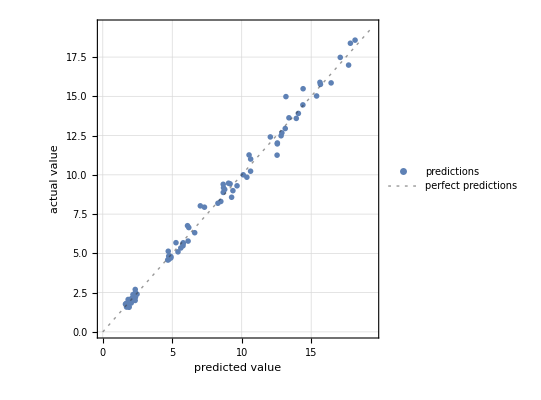

```mathematica
pmGPE["ComparisonPlot"]
```